## Impurity reveals distinct operational phases in quantum thermodynamic cycles: Our paper delves into the quantum Otto and Carnot heat cycles. In the realm of quantum thermodynamics, while others have explored work outputs and efficiencies for various quantum cycles, the impact of impurities has remained unexplored. We’ve introduced an impurity, harnessed quantum thermodynamics, and uncovered intriguing effects. What sets our work apart is the revelation of diverse operational phases by adjusting system parameters: heat engine, cold pump, refrigerator – all achievable. Astonishingly, the addition of an impurity boosts quantum heat engine performance. Our work opens doors to a versatile device, enabling seamless shifts between operational modes. Furthermore, it aligns with current research trends, as unconventional thermodynamic properties of low-dimensional systems garner significant attention.

Work and heat calculation
This code depicts the case when strength of the impurity is varied stroke-wise. This code can be used to reproduce Fig. 8 in the paper. 
Work will be computed using the following expression:
-Graphics-
To calculate this we use the “Sum” function offered by Wolfram Mathematica.

Identifying distinct thermodynamic phases:
Distinct thermodynamic phases can be identified by comparing the relative signs of work done and heat absorbed/emitted as shown in the table below (Table I in the paper):
-Graphics-

Initializing functions
1) ENE: Returns the eigenvalue of the system in weak coupling regime (Eq.15 in the paper) as shown below 
:-Graphics-
2) ZA: Returns the partition function of our system, which is given by:
-Graphics-

```mathematica
ENE[n6_,g6_,p6_,L6_]:=38.19/(L6^2)*((n6*Pi)^2-(4/g6)*((Sin[n6*Pi*p6])^2)-(4/(g6*n6*Pi)^2)*((Sin[n6*Pi*p6])^4+(2*Pi*n6)*(1-2*p6)*((Sin[n6*Pi*p6])^3)*Cos[n6*Pi*p6]));
(*This in electron volt
0.0423 is the value of h^2/2mL^2  in meV ie in milli electron volt where h cut is taken in electrol volt and m is mass of e , L = 30nm**)
(*Now lets define PArtition function for pertubative   ENErgy*)
ZA[p6_,st6_,T6_,L6_]:=Sum[Exp[-(38.19/((L6^2)T6))*((n6*Pi)^2-(4/st6)*((Sin[n6*Pi*p6])^2)-(4/(st6*n6*Pi)^2)*((Sin[n6*Pi*p6])^4+(2*Pi*n6)*(1-2*p6)*((Sin[n6*Pi*p6])^3)*Cos[n6*Pi*p6]))],{n6,1,100}](*Note that Wh  ENEver T is written then the boltzman Constant is also included in it*)
(*Defining Temperature, in all these values boltzman const is included*)
(*if ur temperature is x then put x*0.086173333  *)
```

```mathematica
Initialize Variables
```

```mathematica
atc6 =   0.12926;(* K multiplied by Cold reservoir temperature  here it is 1.5 K*) 
  ath6 =0.43086665;(*Hot reservoir 1 temp *  5K *) 
  ath7 = 1.02546263;(* Hot reservoir 2 temp *11.9K *)
  ath8 =2.1543333;(*Hot reservoir 3 temp *K 25 *)
  asth =1;(*Strength at hot reservoir*)
  astc =-1;(* strength in cold reservoir *)
  k = 0.08617; (*Value of boltzman constant in meV*)
```

Computing Work done while varying position and length of the system cyclewise and strength is varied strokewise

```mathematica
colors={Black,Red,Green,Blue,Cyan,Yellow};

w=List@@@ColorConvert[colors,"RGB"].{0.3,0.3370,0.5}

colorfn=Evaluate[Blend[{w,colors}ᵀ,#]]&;
```

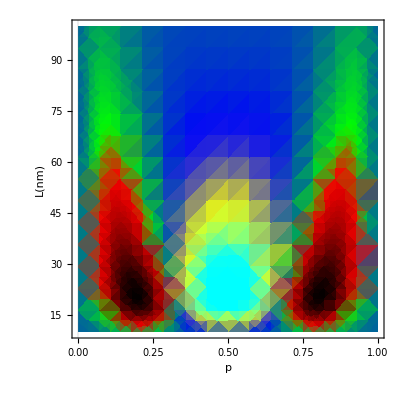

```mathematica
DensityPlot[((Sum[  ENE[n6,asth,p6,L]/(Exp[  ENE[n6,asth,p6,L]/ath8]),{n6,1,100}]/ZA[p6,asth,ath8,L])- (Sum[  ENE[n6,asth,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])-(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,asth,p6,L])/ath8]),{n6,1,100}]/ZA[p6,asth,ath8,L])+(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])),{p6,0,1},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p","L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn]
```

## Varying p (position) and Th (hot reservoir temperature) L = 25nm

```mathematica
L= 25;
```

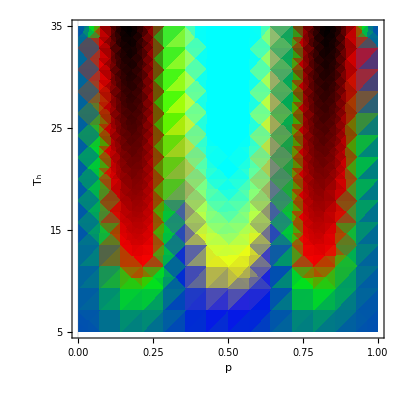

```mathematica
DensityPlot[((Sum[  ENE[n6,asth,p6,L]/(Exp[  ENE[n6,asth,p6,L]/(k*T)]),{n6,1,100}]/ZA[p6,asth,(k*T),L])- (Sum[  ENE[n6,asth,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])-(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,asth,p6,L])/(k*T)]),{n6,1,100}]/ZA[p6,asth,(k*T),L])+(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])),{p6,0,1},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{Automatic,None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn]
```

## Varying f (strength) and T_h (from 1 to 50K)

```mathematica
ph= 0.5;
```

```mathematica
colors={Blue,Cyan,Yellow};

w=List@@@ColorConvert[colors,"RGB"].{0.1,0.3570,0.3}

colorfn2=Evaluate[Blend[{w,colors}ᵀ,#]]&;


(*DensityPlot[x,{x,0,1},{y,0,2},AspectRatio->0.1,ColorFunction->colorfn2]*)
```

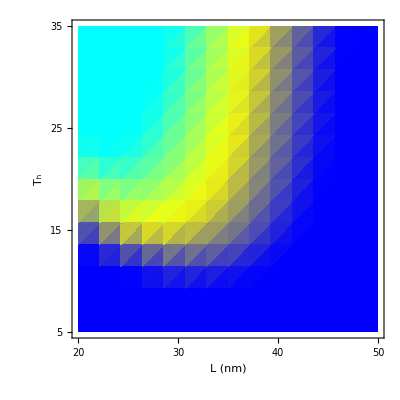

```mathematica
DensityPlot[((Sum[  ENE[n6,asth,ph,Lth]/(Exp[  ENE[n6,asth,ph,Lth]/(k*T)]),{n6,1,100}]/ZA[ph,asth,(k*T),Lth])- (Sum[  ENE[n6,asth,ph,Lth]/(Exp[(  ENE[n6,astc,ph,Lth])/atc6 ]),{n6,1,100}]/ZA[ph,astc,atc6 ,Lth])-(Sum[  ENE[n6,astc,ph,Lth]/(Exp[(  ENE[n6,asth,ph,Lth])/(k*T)]),{n6,1,100}]/ZA[ph,asth,(k*T),Lth])+(Sum[  ENE[n6,astc,ph,Lth]/(Exp[(  ENE[n6,astc,ph,Lth])/atc6 ]),{n6,1,100}]/ZA[ph,astc,atc6 ,Lth])),{Lth,20,50},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{20,30,40,50},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn2]
```

## For Cold Pump , plotting work in the above plot for p (position of impurity) =0.15

```mathematica
ph= 0.15;


colors={Black,Red,Green};

w=List@@@ColorConvert[colors,"RGB"].{0.15,0.77570,0.1}

colorfn3=Evaluate[Blend[{w,colors}ᵀ,#]]&;


(*DensityPlot[x,{x,0,1},{y,0,2},AspectRatio->0.1,ColorFunction->colorfn3]*)
```

{0.,0.15,0.7757}

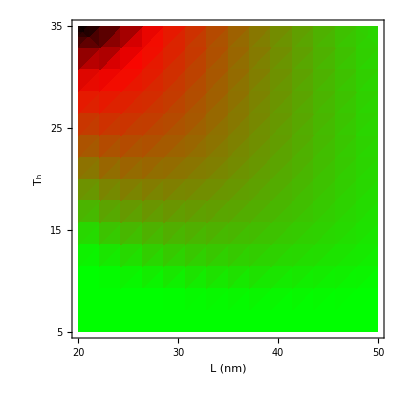

```mathematica
DensityPlot[((Sum[  ENE[n6,asth,ph,Lth]/(Exp[  ENE[n6,asth,ph,Lth]/(k*T)]),{n6,1,100}]/ZA[ph,asth,(k*T),Lth])- (Sum[  ENE[n6,asth,ph,Lth]/(Exp[(  ENE[n6,astc,ph,Lth])/atc6 ]),{n6,1,100}]/ZA[ph,astc,atc6 ,Lth])-(Sum[  ENE[n6,astc,ph,Lth]/(Exp[(  ENE[n6,asth,ph,Lth])/(k*T)]),{n6,1,100}]/ZA[ph,asth,(k*T),Lth])+(Sum[  ENE[n6,astc,ph,Lth]/(Exp[(  ENE[n6,astc,ph,Lth])/atc6 ]),{n6,1,100}]/ZA[ph,astc,atc6 ,Lth])),{Lth,20,50},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{20,30,40,50},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn3]
```

## Computing efficiency while varying p (position of impurity) and L (length of well) cyclewise

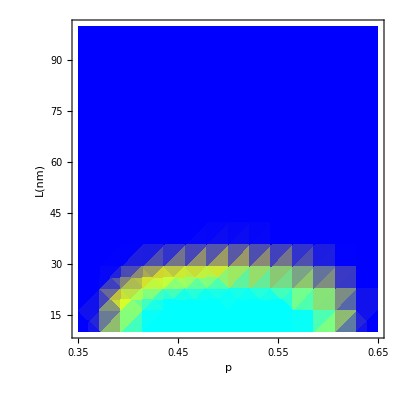

```mathematica
p1 =DensityPlot[((Sum[  ENE[n6,asth,p6,L]/(Exp[  ENE[n6,asth,p6,L]/ath8]),{n6,1,100}]/ZA[p6,asth,ath8,L])- (Sum[  ENE[n6,asth,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])-(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,asth,p6,L])/ath8]),{n6,1,100}]/ZA[p6,asth,ath8,L])+(Sum[  ENE[n6,astc,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L]))/((Sum[  ENE[n6,asth,p6,L]/(Exp[  ENE[n6,asth,p6,L]/ath8]),{n6,1,100}]/ZA[p6,asth,ath8,L])- (Sum[  ENE[n6,asth,p6,L]/(Exp[(  ENE[n6,astc,p6,L])/atc6 ]),{n6,1,100}]/ZA[p6,astc,atc6 ,L])),{p6,0.35,0.65},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p","L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{Automatic,None},{{0.35,0.45,0.55,0.65},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"η"],ColorFunction->colorfn2]
```

## Computing efficiency varying T_h (temperature of hot reservoir) and p (position of impurity)

```mathematica
Lthc = 25;
```

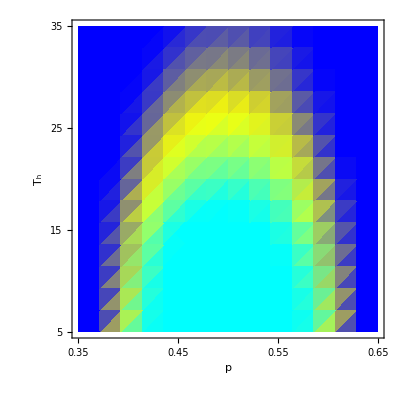

```mathematica
DensityPlot[((Sum[  ENE[n6,asth,p,Lthc]/(Exp[  ENE[n6,asth,p,Lthc]/(k*T)]),{n6,1,100}]/ZA[p,asth,(k*T),Lthc])- (Sum[  ENE[n6,asth,p,Lthc]/(Exp[(  ENE[n6,astc,p,Lthc])/atc6 ]),{n6,1,100}]/ZA[p,astc,atc6 ,Lthc])-(Sum[  ENE[n6,astc,p,Lthc]/(Exp[(  ENE[n6,asth,p,Lthc])/(k*T)]),{n6,1,100}]/ZA[p,asth,(k*T),Lthc])+(Sum[  ENE[n6,astc,p,Lthc]/(Exp[(  ENE[n6,astc,p,Lthc])/atc6 ]),{n6,1,100}]/ZA[p,astc,atc6 ,Lthc]))/((Sum[  ENE[n6,asth,p,Lthc]/(Exp[  ENE[n6,asth,p,Lthc]/(k*T)]),{n6,1,100}]/ZA[p,asth,(k*T),Lthc])- (Sum[  ENE[n6,asth,p,Lthc]/(Exp[(  ENE[n6,astc,p,Lthc])/atc6 ]),{n6,1,100}]/ZA[p,astc,atc6 ,Lthc])),{p,0.35,0.65},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{0.35,0.45,0.55,0.65},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"η"],ColorFunction-> colorfn2]
```